9.81

10

0.1

0.01

0.015

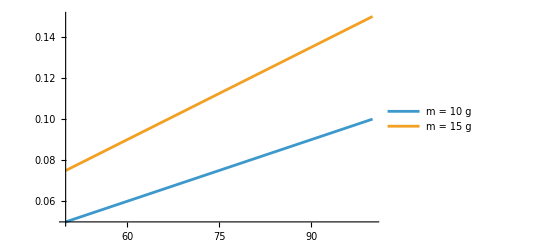

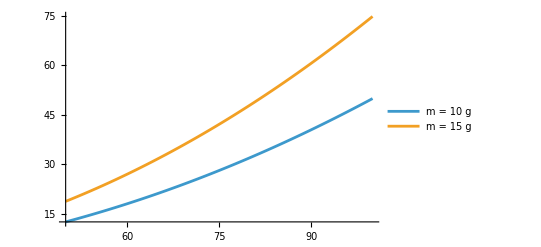

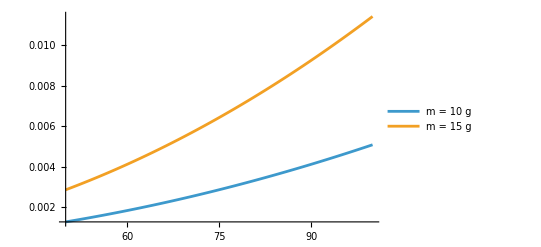

```mathematica
ClearAll["Global`*"]
g=9.81
M=10(*kg*)
k=0.1
m1=0.01
m2=0.015
(*zasada zachowania pędu*)
vu[vp_,m_]:=m*vp/(M+m)
Q[vp_,m_]:=(0.5*m*vp^2)-(0.5*(M+m)*vu[vp,m]^2)
s[vp_,m_]:=(vu[vp,m]^2)/(2*k*g)
(**)
Plot[{vu[v,m1],vu[v,m2]},{v,50,100},PlotLegends->{"m = 10 g","m = 15 g"}]
Plot[{Q[v,m1],Q[v,m2]},{v,50,100},PlotLegends->{"m = 10 g","m = 15 g"}]
Plot[{s[v,m1],s[v,m2]},{v,50,100},PlotLegends->{"m = 10 g","m = 15 g"}]
```